#### Function list dump

pipe
pipeList
branch
branchSeq
deCurry
nativeSize
checkerboard
gammaDecode
gammaEncode
imgGammaDecode
imgGammaEncode
levelIndentFunc
horizontalTreeForm
GraphEdgeSleek
toRegularArray
inputHistoryViewer
StringSplitNested
colorFromHex
colorToHex
DatasetGrid

```mathematica
Needs["SilviaCollection`"]
```

```mathematica
x//pipe[f,h,g]
```

g[h[f[x]]]

```mathematica
x//pipeList[f,h,g]
```

{x,f[x],h[f[x]],g[h[f[x]]]}

```mathematica
x//branch[f,h,g]
```

{f[x],h[x],g[x]}

```mathematica
x//branchSeq[f,h,g]//F
```

F[f[x],h[x],g[x]]

```mathematica
f[1,2,3,4]//deCurry
```

f[1][2][3][4]

Gamma correction is important:

```mathematica
{
ConstantImage[RGBColor[0.1725, 0.5767499999999999, 0.75],{101,101}]
,ConstantImage[RGBColor[0.88, 0.2024, 0.2024],{101,101}]
,Image[GaussianMatrix[{50,30}]//Rescale]
}//pipeList[
branch[First,pipe[Rest,Apply@SetAlphaChannel]]
,branch[Identity,Map@pipe[branchSeq[pipe[RemoveAlphaChannel,imgGammaDecode],AlphaChannel],SetAlphaChannel]]
,ImageCompose@@@#&,Map@RemoveAlphaChannel
,branch[First,pipe[Last,imgGammaEncode]]
]//pipe[
Rest,Append[{"↑ wrong blend","↑ correct blend"}]
,Grid[#,Frame->All,ItemSize->Full]&
]
```

-Graphics- | -Graphics-
{-Graphics-,-Graphics-} | {-Graphics-,-Graphics-}
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
↑ wrong blend | ↑ correct blend

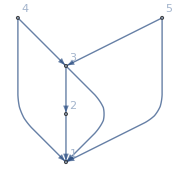

```mathematica
mygraph=Graph[{1,2,3,4,5},{2->1,3->1,3->2,4->1,4->3,5->1,5->3},VertexLabels->"Name",ImageSize->Small]
```

```mathematica
mygraph//GraphEdgeSleek
```

-Graphics-